```mathematica
Solve[x == y + T/2 Sqrt[a(z+x)] ,x]
```

{{x→1/8 (a T^2+8 y-√a T √(a T^2+16 y+16 z))},{x→1/8 (a T^2+8 y+√a T √(a T^2+16 y+16 z))}}

```mathematica
Sqrt[16]
```

4

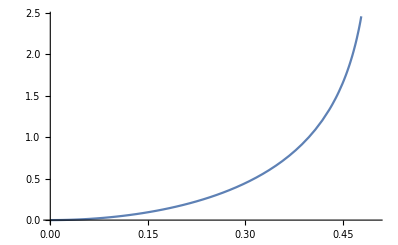

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

```mathematica
Plot[-Log[1-4*Epsilon^2],{Epsilon,0,.5}]
```

This is when alpha will be smaller than 1 (ie sqrt(alpha) > alpha)

```mathematica
N[Solve[-Log[1-4*Epsilon^2]==1,Epsilon]]
```

{{Epsilon→-0.39753},{Epsilon→0.39753}}

By theorem B2 in Auer the regret (for the bandit) case is:

```mathematica
a(T - T/K - T/2Sqrt[-T/K Log[1-4a^2]])
```

a (T-T/K-1/2 T √(-(T Log[1-4 a^2])/K))

For small epsilon, expand as a Taylor series

```mathematica
Series[a (T-T/K-1/2 T √(-(T Log[1-4 a^2])/K)),{a,0,2}]
```

(T-T/K) a-T √(T/K) a^2+O[a]^3

```mathematica
Simplify[Solve[D[(T-T/K) a-T √(T/K) a^2,a]==0,a]]
```

{{a→((-1+K) √(T/K))/(2 T)}}

This does not exactly match what is in the Auer paper, hmmm, either way we get that to minimize it, a should be approximately sqrt(K/T)

```mathematica
T a - T a^2 Sqrt[T/K]
```

a T-a^2 T √(T/K)

```mathematica
If we work with what Auer gets
```

```mathematica
Simplify[Solve[D[a T-a^2 T √(T/K),a]==0,a]]
FullSimplify[a T-a^2 T √(T/K)/.a->1/(2 √(T/K))]
```

{{a→1/(2 √(T/K))}}

1/4 K √(T/K)

```mathematica
I seem to get for the non-bandit case
```

```mathematica
a(T - T/K) - (a+T/2)(T/2)Sqrt[-T/K Log[1-4a^2]]
```

```mathematica
a (T-T/K)-1/2 (a+T/2) T √(-(T Log[1-4 a^2])/K)
```

If we work with this:

```mathematica
Series[a (T-T/K)-1/2 (a+T/2) T √(-(T Log[1-4 a^2])/K),{a,0,2}]
```

(T-T/K-1/2 T^2 √(T/K)) a-T √(T/K) a^2+O[a]^3

```mathematica
Plot3D[(T-T/K-1/2 T^2 √(T/K)) a-T √(T/K) a^2 /.a->.1,{T,1,100},{K,2,10}]
```

-Graphics3D-

```mathematica
Plot3D[a (T-T/K)-1/2 (a+T/2) T √(-(T Log[1-4 a^2])/K)/.a->0.1,{T,1,100},{K,2,10}]
```

-Graphics3D-

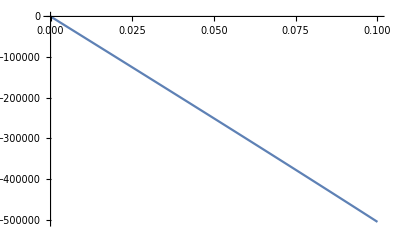

```mathematica
Plot[a (T-T/K)-1/2 (a+T/2) T √(-(T Log[1-4 a^2])/K)/.{T->1000,K->10},{a,0,.1}]
```

90 a-50 √10 (50+a) √(-Log[1-4 a^2])

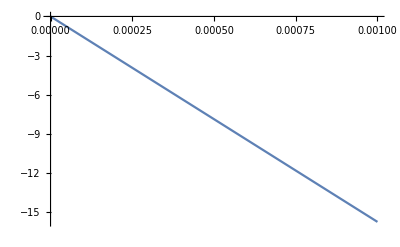

```mathematica
Simplify[a (T-T/K)-1/2 (a+T/2) T √(-(T Log[1-4 a^2])/K)/.{T->100,K->10}]
```

```mathematica
FindMaximum[{90 a-50 √10 (50+a) √(-Log[1-4 a^2]),a < 1,a>0},a]
```

FindMaximum::nrnum: The function value 8802.8  - 11452.4\ ⅈ is not a real number at {a} = {0.9}.

FindMaximum[{90 a-50 √10 (50+a) √(-Log[1-4 a^2]),a<1,a>0},a]

```mathematica
Simplify[Solve[D[(T-T/K-1/2 T^2 √(T/K)) a-T √(T/K) a^2,a]==0,a]]
```

```mathematica
{{a->-(√(T/K) (2+K (-2+T √(T/K))))/(4 T)}}
```

{{a→-49991/200}}

```mathematica
Simplify[Solve[D[(T-1/2 T^2 √(T/K)) a-T √(T/K) a^2,a]==0,a]]
```

{{a→-T/4+1/(2 √(T/K))}}

```mathematica
Simplify[(T-T/K-1/2 T^2 √(T/K)) a-T √(T/K) a^2 /. a->1/2Sqrt[K/T]]
```

```mathematica
N[-1/4 K √(T/K)-(2+K (-2+T √(T/K)))/(4 √(K/T))/.{T->100,K->10}]
```

-249980.

```mathematica
Maximize[{(T-T/K-1/2 T^2 √(T/K)) a-T √(T/K) a^2,a > 0},a]
```

{Piecewise[{{(4 T^2-4 K T^2+K √((T (4-8 K+4 K^2+K T^3)^2)/K^3))/(16 K), T>0&&K>1/8 (8+T^3)+1/8 √(16 T^3+T^6)}, {-∞, !((T==0&&K>0)||(T==0&&K<0)||(T>0&&0<K≤1/8 (8+T^3)+1/8 √(16 T^3+T^6))||(T>0&&K>1/8 (8+T^3)+1/8 √(16 T^3+T^6))||(T<0&&K<0))}, {∞, T<0&&K<0}, {0, True}}],{a→Piecewise[{{1, (T==0&&K>0)||(T==0&&K<0)}, {Indeterminate, !((T==0&&K>0)||(T==0&&K<0)||(T>0&&K>1/8 (8+T^3)+1/8 √(16 T^3+T^6)))}, {Root[64 T-(16 T)/K-96 K T+64 K^2 T-16 K^3 T-24 T^4+48 K T^4-24 K^2 T^4-K T^7-8 K T^2 √((T (4-8 K+4 K^2+K T^3)^2)/K^3)+8 K^2 T^2 √((T (4-8 K+4 K^2+K T^3)^2)/K^3)+(-128 T^3+256 K T^3-128 K^2 T^3-32 K T √((T (4-8 K+4 K^2+K T^3)^2)/K^3)+32 K^2 T √((T (4-8 K+4 K^2+K T^3)^2)/K^3)) #1+(-256 T^2+512 K T^2-256 K^2 T^2+64 K T^5) #1^2+256 K T^4 #1^3+256 K T^3 #1^4&,3], True}}]}}

Going back to where we still have E_unif[N_0] involved - represent with N0

```mathematica
R > T N0/2 + a(T-T/K)-(a+T/2)(T/2)Sqrt[-Log[1-4a^2](T/K + N0)]
```

(-1/K+T) ϵ>(N0 T)/2+a (T-T/K)-1/2 (a+T/2) T √(-(N0+T/K) Log[1-4 a^2])

```mathematica
Plot3D[(N0 T)/2+a (T-T/K)-1/2 (a+T/2) T √(-(N0+T/K) Log[1-4 a^2])/. {a->0.1,T->1000},{K,2,10},{N0,1,100}]
```

-Graphics3D-

What about if we look at the standard bandit case in this way ...

```mathematica
a(T - T/K - T/2Sqrt[-T/K Log[1-4a^2]])
```

a (T-T/K-1/2 T √(-(T Log[1-4 a^2])/K))

```mathematica
Series[a (T-T/K-1/2 T √(-(T Log[1-4 a^2])/K)),{a,0,2}]
```

(T-T/K) a-T √(T/K) a^2+O[a]^3

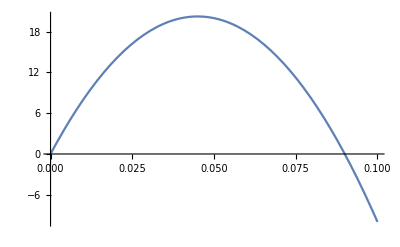

```mathematica
(T-T/K) a-T √(T/K) a^2+O[a]^3
Plot[(T-T/K) a-T √(T/K) a^2/.{K->10,T->1000},{a,0,.1}]
```

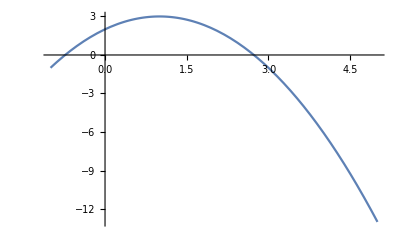

-1.

```mathematica
Plot[a x^2+b x+ c/.{a->-1,b->2,c->2},{x,-1,5}]
N[2/2(-1)]
```

```mathematica
Plot3D[a (T-T/K-1/2 T √(-(T Log[1-4 a^2])/K))/.{a->.5Sqrt[K/T]},{K,2,10},{T,1,1000}]
```

-Graphics3D-

```mathematica
N[Sqrt[10/1000]]
```

0.1

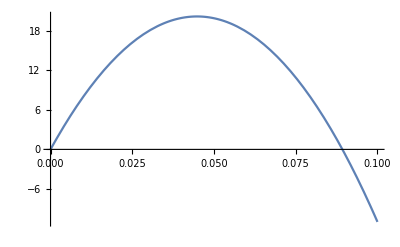

```mathematica
Plot[a (T-T/K-1/2 T √(-(T Log[1-4 a^2])/K)) /.{K->10,T->1000},{a,0,.1}]
```

```mathematica
N0 - T/2Sqrt[-Log[1-4a^2](T/K + N0)]

Series[N0 - T/2Sqrt[-Log[1-4a^2](T/K + N0)],{a,0,2}]
```

```mathematica
N0-1/2 T √(-(N0+T/K) Log[1-4 a^2]) /. a-> 1/2Sqrt[K/T]
```

N0-1/2 T √((-N0-T/K) Log[1-K/T])

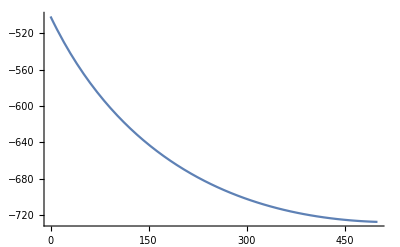

```mathematica
Plot[N0-1/2 T √((-N0-T/K) Log[1-K/T])/.{T->1000,K->10},{N0,0,500}]
```

```mathematica
N0-T √((K N0+T)/K) a+O[a]^3
Solve[D[N0-T √((K N0+T)/K) a,a] ==0,a]
```

N0-T √((K N0+T)/K) a+O[a]^3

{{}}

```mathematica
Plot3D[N0-1/2 T √(-(N0+T/K) Log[1-4 a^2])/.{T->1000,K->10},{N0,0,500},{a,0,.1}]
```

-Graphics3D-

```mathematica
Simplify[N0-1/2 T √(-(N0+T/K) Log[1-4 a^2])/.{T->1000,K->10}]
```

```mathematica
N0-500 √(-(100+N0) Log[1-4 a^2])/.N0->10
FindMaximum[{10-500 √110 √(-Log[1-4 a^2]),a>0,a<.5},a]
```

```mathematica
10-500 √110 √(-Log[1-4 a^2])
Plot[10-500 √110 √(-Log[1-4 a^2]),{a,0,.01}]
```

10-500 √110 √(-Log[1-4 a^2])

```mathematica
Series[N0-500 √(-(100+N0) Log[1-4 a^2]),{a,0,2}]
```

N0-1000 √(100+N0) a+O[a]^3

```mathematica
FindMaximum[{10-500 √110 √(-Log[1-4 a^2]),a>0,a<1},a]
Plot[-Log[1-4 a^2],{a,0,1}]
```

FindMaximum::nrnum: The function value 5778.65  - 7462.34\ ⅈ is not a real number at {a} = {0.9}.

FindMaximum[{10-500 √110 √(-Log[1-4 a^2]),a>0,a<1},a]

```mathematica
values = List[0,10,100,1000]
```

{0,10,100,1000}

```mathematica
Do[Print[i^2],{i,values}]
```

0

100

10000

1000000

{0,10,100,1000}

```mathematica
a(T - T/K - T/2Sqrt[-1/K Log[1-4a^2](T+K*T)])
Series[a(T - T/K - T/2Sqrt[-1/K Log[1-4a^2](T+K*T)]),{a,0,2}]
```

a (T-T/K-1/2 T √(-((T+K T) Log[1-4 a^2])/K))

(T-T/K) a-T √(((1+K) T)/K) a^2+O[a]^3

```mathematica
Solve[D[(T-T/K) a-T √(((1+K) T)/K) a^2,a]==0,a]
```

{{a→(-1+K)/(2 K √(((1+K) T)/K))}}

```mathematica
Simplify[(T-T/K) a-T √(((1+K) T)/K) a^2 /.a->(-1+K)/(2 K √(((1+K) T)/K))]
```

((-1+K)^2 T)/(4 K^2 √((1+1/K) T))

```mathematica
(T/2)N0 + a(T - T/K) - (a+T/2)(T/2)Sqrt[-Log[1-4a^2](T/K + N0)]
```

(N0 T)/2+a (T-T/K)-1/2 (a+T/2) T √(-(N0+T/K) Log[1-4 a^2])

```mathematica
Series[(T/2)N0 + a(T - T/K) - (a+T/2)(T/2)Sqrt[-Log[1-4a^2](T/K + N0)],{a,0,2}]
```

(N0 T)/2+(T-T/K-1/2 T^2 √((K N0+T)/K)) a-T √((K N0+T)/K) a^2+O[a]^3

```mathematica
Simplify[-(T-T/K-1/2 T^2 √((K N0+T)/K)) /2(T √((K N0+T)/K))]
```

(T^2 √(N0+T/K) (2+K (-2+T √(N0+T/K))))/(4 K)

```mathematica
Simplify[Solve[D[(N0 T)/2+(T-1/2 T^2 √((K N0+T)/K)) a-T √((K N0+T)/K) a^2,a]==0,a]]
```

{{a→-T/4+(K √(N0+T/K))/(2 (K N0+T))}}

```mathematica
Simplify[(N0 T)/2+(T-1/2 T^2 √((K N0+T)/K)) a-T √((K N0+T)/K) a^2/.a->-T/4+(K √(N0+T/K))/(2 (K N0+T))]
```

(8 N0 T^2+T^3 (-4+T √(N0+T/K))+K (8 N0^2 T+4 T √(N0+T/K)+N0 T^2 (-4+T √(N0+T/K))))/(16 (K N0+T))

```mathematica
Plot3D[(8 N0 T^2+T^3 (-4+T √(N0+T/K))+K (8 N0^2 T+4 T √(N0+T/K)+N0 T^2 (-4+T √(N0+T/K))))/(16 (K N0+T))/. {T->100},{N0,0,100},{K,2,30}]
```

-Graphics3D-

```mathematica
Simplify[(8 N0 T^2+T^3 (-4+T √(N0+T/K))+K (8 N0^2 T+4 T √(N0+T/K)+N0 T^2 (-4+T √(N0+T/K))))/(16 (K N0+T))/.N0->0]
```

1/16 (-4 T^2+4 K √(T/K)+T^3 √(T/K))

```mathematica
Solve[T^2/3 == 2Sqrt[K],T]
```

{{T→-√6 K^(1/4)},{T→√6 K^(1/4)}}

```mathematica
Plot3D[(-2+2 K-K T √((K N0+T)/K))/(4 K √((K N0+T)/K))/.N0->10,{K,2,10},{T,1,100}]
```

-Graphics3D-

```mathematica
Simplify[(N0 T)/2+(T-T/K-1/2 T^2 √((K N0+T)/K)) a-T √((K N0+T)/K) a^2,(-2+2 K-K T √((K N0+T)/K))/(4 K √((K N0+T)/K))]
```

(K N0 T-2 a^2 K T √(N0+T/K)-a T (2+K (-2+T √(N0+T/K))))/(2 K)

```mathematica
Series[-Log[1-4a^2],{a,0,2}]
```

4 a^2+O[a]^3

```mathematica
a(T - T/K - T/2Sqrt[-Log[1-4a^2](T/K+N0)]) + T/2 N0
```

(N0 T)/2+a (T-T/K-1/2 T √(-(N0+T/K) Log[1-4 a^2]))

```mathematica
Series[(N0 T)/2+a (T-T/K-1/2 T √(-(N0+T/K) Log[1-4 a^2])),{a,0,2}]
```

(N0 T)/2+(T-T/K) a-T √((K N0+T)/K) a^2+O[a]^3

```mathematica
Solve[D[(N0 T)/2+(T) a-T √((K N0+T)/K) a^2,a]==0,a]
```

{{a→1/(2 √((K N0+T)/K))}}

```mathematica
(N0 T)/2+(T) a-T √((K N0+T)/K) a^2/.a->1/(2 √((K N0+T)/K))
```

(N0 T)/2+T/(2 √((K N0+T)/K))-(K T √((K N0+T)/K))/(4 (K N0+T))

```mathematica
Simplify[((N0 T)/2+(T) a-T √((K N0+T)/K) a^2)/.a->1/(2 √((K N0+T)/K))]
```

(N0 T)/2+(K T √(N0+T/K))/(4 (K N0+T))

```mathematica
Solve[D[(N0 T)/2+T/(2 √((K N0+T)/K))-(K T √((K N0+T)/K))/(4 (K N0+T)),N0] == 0,N0]
```

{{N0→(2^(2/3) K-4 T)/(4 K)}}

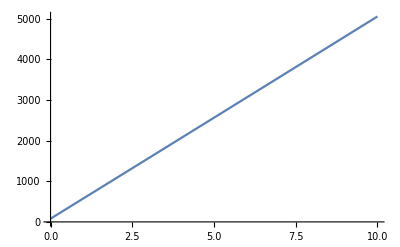

```mathematica
Plot[(N0 T)/2+(K T √(N0+T/K))/(4 (K N0+T))/.{T->1000,K->100},{N0,0,10}]
```

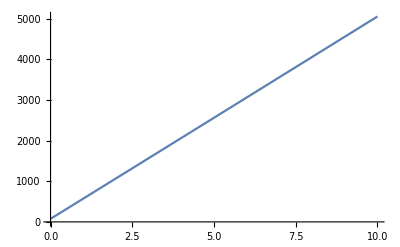

```mathematica
Plot[(N0 T)/2+a (T-T/K-1/2 T √(-(N0+T/K) Log[1-4 a^2]))//.{a->1/(2 √((K N0+T)/K)),T->1000,K->100},{N0,0,10}]
```

```mathematica
Simplify[Solve[D[(N0 T)/2+(K T √(N0+T/K))/(4 (K N0+T)),N0]==0,N0]]
```

{{N0→1/4 (2^(2/3)-(4 T)/K)}}

```mathematica
Simplify[Reduce[1/4 (2^(2/3)-(4 T)/K) > 0,T]]
```

(K<0&&4 T>2^(2/3) K)||(K>0&&4 T<2^(2/3) K)

Basically seems to imply this will be minimized with N0 = 0 unless T < K ... That does not seem right....

Ok so a quadratic about N0 = 0 is a bad approximation - not really sure why when the function looks so linear, anyway ....

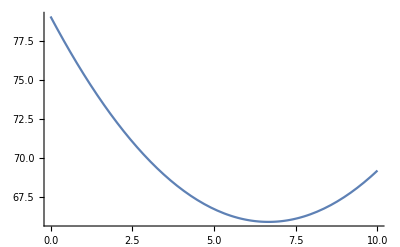

```mathematica
Plot[1/4 K √(T/K)-((K^2 √(T/K)) N0)/(8 T)+(3 K^3 √(T/K) N0^2)/(32 T^2)//.{T->1000,K->100},{N0,0,10}]
```

```mathematica
Series[(K T √(N0+T/K))/(4 (K N0+T)),{N0,0,2}]
```

1/4 K √(T/K)-((K^2 √(T/K)) N0)/(8 T)+(3 K^3 √(T/K) N0^2)/(32 T^2)+O[N0]^3

```mathematica
Solve[D[1/4 K √(T/K)-((K^2 √(T/K)) N0)/(8 T)+(3 K^3 √(T/K) N0^2)/(32 T^2),N0]==0,N0]
```

{{N0→(2 T)/(3 K)}}

```mathematica
Series[(N0 T)/2+(K T √(N0+T/K))/(4 (K N0+T)),{N0,0,2}]
```

1/4 K √(T/K)+(T/2-(K^2 √(T/K))/(8 T)) N0+(3 K^3 √(T/K) N0^2)/(32 T^2)+O[N0]^3

```mathematica
Simplify[Solve[D[1/4 K √(T/K)+(T/2-(K^2 √(T/K))/(8 T)) N0+(3 K^3 √(T/K) N0^2)/(32 T^2),N0]==0,N0]]
```

{{N0→(2 T (K-4 T √(T/K)))/(3 K^2)}}

```mathematica
Reduce[(2 T K)/(3 K^2)>(4 T √(T/K))/(3 K^2),T]
```

(K<0&&T<0)||(K>0&&0<T<K^3/4)

```mathematica
N[1000^(1/3)]
```

10.